```mathematica
Clear[x];
Clear[y];
Solve[{x-2y==-1,  3y-x==3}, {x, y}]
```

{{x→3,y→2}}

```mathematica
ContourPlot[{x-2y==-1,  -x+2y==3}, {x, 0, 5}, { y, 0, 3}, GridLines->None, Frame->False, Axes->True, ContourLabels->True, FrameLabel->None]
(* No solutions *)
```

-Graphics-

```mathematica
ContourPlot[{x-2y==-1,  -x+2y==1}, {x, 0, 5}, { y, 0, 3}, GridLines->None, Frame->False, Axes->True, ContourLabels->True, FrameLabel->None]
(* Infinite number of solutions *)
```

-Graphics-

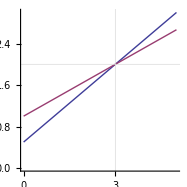

{True,True}

```mathematica
ContourPlot[{x-2y==-1,  3y-x==3}, {x, 0, 5}, { y, 0,3}, GridLines->{{3},{2}}, GridLinesStyle->LightGray, Frame->False, Axes->True, ContourLabels->True, FrameLabel->None]
(* x = 3 and y = 2. ContourPlot treats the variables x and y as local -- effectively using Block *)
x=3;y= 2;{x-2y==-1,  3y-x==3}
```

```mathematica
Clear[x];
Clear[y];
```